# Sample Kinetic Fitting

## Importing data into variables

The first step in enzyme kinetic data fitting is to import the data, requiring the correct file path. The text data = tells Mathematica to store your imported data in a variable called “data.” 

If you are using the app, you can type Import[“ and after you add that last “ you’ll see a button called “File Browser.” Click on that to locate your data file. 

Otherwise, you can have Mathematica add the file path by going through the Insert tab, followed by “File Path...”

Put //TableForm at the end of the line to get the data to display in columns.  Hit ⇧ + ⌤ to execute the command.

```mathematica
data = Import["/Users/tstack/Desktop/kinetics.csv"]//TableForm (* Text like this that is between parentheses and asterisks is ignored by Mathematica when you hit Shift-Enter to execute code. *)
```

[Sub] | v/E
2.4 | 0.770713
3.75 | 0.963391
6 | 1.15607
9 | 2.11946
15 | 2.60116
24 | 3.66089
37.5 | 5.68401
60 | 4.91329
2.4 | 0.770713
3.75 | 0.770713
6 | 1.15607
9 | 1.83044
15 | 2.89017
24 | 4.14258
37.5 | 5.97303
60 | 5.97303
2.4 | 0.578035
3.75 | 0.963391
6 | 1.25241
9 | 1.63776
15 | 2.79383
24 | 4.72062
37.5 | 4.81696
60 | 5.29865
[Sub] | avg v/E
2.4 | 0.706487
3.75 | 0.899165
6 | 1.18818
9 | 1.86256
15 | 2.76172
24 | 4.17469
37.5 | 5.49133
60 | 5.39499

Now select the rows for the average data and copy/paste to define that data sets (repeating for the full data). Adding a semicolon after the end of the commands tells Mathematica “do not display the output.” Notice that the variables avgData and fullData are shown in blue type until you hit ⇧ + ⌤, at which point they become black. The black type indicates that the variable now has a value.

```mathematica
avgData={{2.4, 0.7064868}, {3.75, 0.8991651}, {6, 1.1881824}, {9, 1.8625562}, {15, 2.7617213}, {24, 4.1746949}, {37.5, 5.4913295}, {60, 5.3949904}};(* The ' symbol after some numbers indicates that there are more digits than shown on screen *)
fullData={{2.4, 0.7707129}, {3.75, 0.9633911}, {6, 1.1560694}, {9, 2.1194605}, {15, 2.6011561}, {24, 3.6608863}, {37.5, 5.6840077}, {60, 4.9132948}, {2.4, 0.7707129}, {3.75, 0.7707129}, {6, 1.1560694}, {9, 1.8304432}, {15, 2.8901734}, {24, 4.1425819}, {37.5, 5.973025}, {60, 5.973025}, {2.4, 0.5780347}, {3.75, 0.9633911}, {6, 1.2524085}, {9, 1.6377649}, {15, 2.7938343}, {24, 4.7206166}, {37.5, 4.8169557}, {60, 5.2986513}};
```

## Define the model and plot the results

Next define the nonlinear modified Michaelis Menten equation used in the data fitting. Check again that once executed the "ModifiedMM" turns from blue to black in color, while the substrate concentration "s" and the kinetic constants remain blue (as these are the variables).

```mathematica
ModifiedMM=kcat/(1+kcat/(ksp * s));
```

Below, the first command generates a model equation that fits the observed average data, requiring that kcat and ksp are positive numbers. The following command then reports the parameters as estimates and includes the standard error.

```mathematica
Model=NonlinearModelFit[avgData,{ModifiedMM,kcat>0,ksp>0},{kcat,ksp},s];
modeldata=Model["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047

It is easiest to tell the quality of the fit by plotting the data and the modeled equation on a single graph.

The Show command allows you to show more than one thing on a single graph. In this case, we show a ListPlot[] with every data trial (fullData) to give some sense of the variability and use Plot[]to show the fitted equation. PlotRange automatically defines the x and y axis boundaries using the maximum values of those data.  Remember to change the FrameLabel title to match the name of the substrate. To make sure the data plot automatically scales, there is a variable “sMax” that is defined to be 10% greater than the maximum concentration in the full data.

66.

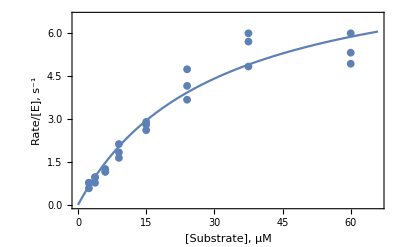

```mathematica
sMax=1.1*Max[fullData[[All,1]]]
Show[
ListPlot[fullData,
(*the following 3 options affect the format of the ListPlot*)PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},
Frame->True,PlotMarkers->{Automatic,8},
FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],
Plot[Model[s],{s,0,sMax}],LabelStyle->Directive[Bold,Medium]]
```

The NonLinearModelFit includes limits to k_cat and k_sp, indicating that they need to be greater than 0. If these bounds alone do not provide a good fit (i.e., the errors are large compared to the estimated parameters), add to or change these bounds so the model finds the true best fit. Recall that k_cat indicates the upper limit of the velocity, and that k_sp represent the initial linear portion of the curve. The command below demonstrates how to change the upper and lower bounds of the variables.

```mathematica
Model=NonlinearModelFit[avgData,{ModifiedMM,kcat>4,kcat<20,ksp>0.01,ksp<5},{kcat,ksp},s];
modeldata=Model["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047

Sometimes Mathematica will not display the full curve from 0 to the final value. I get around this by either plotting the curve twice with two different ranges can circumvent this issue, or fitting the data to a much broader range than visualized in the Plot.

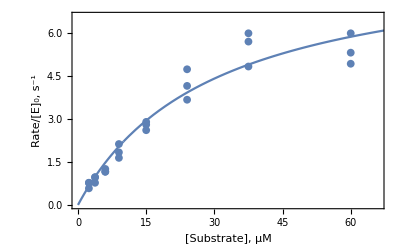

```mathematica
Show[ListPlot[{fullData},PlotRange->{{0,1.1*Max[fullData[[All,1]]]},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E]_0, s^-1"}],Plot[{Model[S]},{S,0,10}],Plot[{Model[S]},{S,10,sMax}],LabelStyle->Directive[Bold,Medium]]
```

## Use data from the model

The code below extracts the best fit values and standard error for k_cat and k_spfrom the table modeldata.

```mathematica
modeldata(*showing the table again as a reminder*)
```

| Estimate | Standard Error | t-Statistic | P-Value
kcat | 8.74556 | 1.11101 | 7.8717 | 0.000222538
ksp | 0.294779 | 0.0416145 | 7.08357 | 0.000397047

To make your calculations easier, copy/paste the values from the table to define your determined values and corresponding errors.

```mathematica
kcatbestfitvalue=8.745560188093302;
kspbestfitvalue=0.29477938924225716;
kcatstandarderror=1.1110132625333924;
kspstandarderror=0.04161453957010604;
```

Note that the units on these values depend on your axes. Here I have plotted substrate concentration in µM and the rate in s^-1. The calculations below are to demonstrate how to report the kinetic constants. With these units, then k_cat has units of s^-1and k_sp has units of µM^-1s^-1. The first calculation determines K_m in units of µM.

```mathematica
Kmbestfitvalue=kcatbestfitvalue/kspbestfitvalue;
out1=Row[{"Km = ",Kmbestfitvalue," µM"}];
TextCell[out1,CellFrame->True]
```

Km = 29.6682 µM

The next calculation determines the error in K_m using error propagation from k_cat and k_sp.

```mathematica
Kmstandarderror=Kmbestfitvalue*√((kcatstandarderror/kcatbestfitvalue)^2+(kspstandarderror/kspbestfitvalue)^2);
out2=Row[{"Km std error = ",Kmstandarderror," µM"}];
TextCell[out2,CellFrame->True]
```

Km std error = 5.63445 µM

Now lets convert the k_spand its error so it has units of M^-1s^-1.

```mathematica
kspSF=ScientificForm[kspbestfitvalue*10^6];
out3=Row[{"ksp = ",kspSF," M-1s-1"}];
TextCell[out3,CellFrame->True]
```

ksp = 2.94779×10^5 M-1s-1

```mathematica
kspSFerror=ScientificForm[kspstandarderror*10^6];
out4=Row[{"ksp std error = ",kspSFerror," M-1s-1"}];
TextCell[out4,CellFrame->True]
```

ksp std error = 4.16145×10^4 M-1s-1

The kinetic values are reported as:
 k_cat = 9 ± 1 s^-1
	K_m = 30. ± 6 μM
	k_sp = 2.9 ± 0.4 × 10^5 M^-1 s^-1

Now lets calculate percent errors to determine how the size of the errors compare to the determined values

```mathematica
kcatpercenterror=100*kcatstandarderror/kcatbestfitvalue;
out5=Row[{"kcat percent error = ",kcatpercenterror," %"}];
TextCell[out5,CellFrame->True]
Kmpercenterror=100*Kmstandarderror/Kmbestfitvalue;
out6=Row[{"Km percent error = ",Kmpercenterror," %"}];
TextCell[out6,CellFrame->True]
ksppercenterror=100*kspstandarderror/kspbestfitvalue;
out7=Row[{"ksp percent error = ",ksppercenterror," %"}];
TextCell[out7,CellFrame->True]
```

kcat percent error = 12.7037 %

Km percent error = 18.9916 %

ksp percent error = 14.1172 %

A great dataset has less than 10% error, and this is pretty close.  A good data set is 15-20% error. Better data could potentially be achieved by using the estimated value of Km to determine the range of concentrations to test as described in the main text.

```mathematica
(* Below is an alternative equation to use in cases of cooperativity, using the Hill equation. This introduces the Hill coefficient, n, which is dimensionless. Note that this equation does not rely on Km but Subscript[K, half] instead, so the specificity constant is different (Subscript[k, SPH] = Subscript[k, cat]/Subscript[K, half]). *)
```

```mathematica
Hill=(kcat)/(1+(kcat/(kspH*S))^n);
```

```mathematica
(* Below is another alternative equation to use in cases of substrate inhibition. This intruduces the inhibition constant, Subscript[K, I], which has units of concentration. *)
```

```mathematica
SubInh=(kcat)/(1+kcat/(ksp*S)+S/KI);
```

```mathematica
(* If saturating levels of substrate are not reached, the data will be best fit by a straight line. In that case, the slope of the line provides the value of and Subscript[k, SP], but does not determine estimates Subscript[k, cat] or Subscript[K, m] in this case. The slope is provided by the "S" estimate*)
```

```mathematica
LinearModel=LinearModelFit[avgData,S,S];
LinearModel[{"BestFitParameters","ParameterTable"}]
HillModel=NonlinearModelFit[avgData,{Hill, kcat>0,kspH>0,n>0},{kcat,kspH,n},S];
HillModel[{"BestFitParameters","ParameterTable"}]
SubInhModel=NonlinearModelFit[avgData,{SubInh, kcat>0,ksp>0,KI>0,kcat<50,KI>10},{kcat,ksp,KI},S];
SubInhModel[{"BestFitParameters","ParameterTable"}]
```

{{1.02342,0.0906551}, | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02342 | 0.418963 | 2.44274 | 0.0502839
S | 0.0906551 | 0.0153702 | 5.89811 | 0.00105503}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→6.72225,kspH→0.390078,n→1.38322}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 6.72225 | 0.935269 | 7.18751 | 0.000811537
kspH | 0.390078 | 0.0535233 | 7.28801 | 0.000761056
n | 1.38322 | 0.268511 | 5.15145 | 0.00361051}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{kcat→49.9998,ksp→0.22558,KI→13.8514}, | Estimate | Standard Error | t-Statistic | P-Value
kcat | 49.9998 | 86.4483 | 0.578378 | 0.588082
ksp | 0.22558 | 0.0256364 | 8.79924 | 0.000314617
KI | 13.8514 | 28.6328 | 0.483759 | 0.648999}

```mathematica
(* The best model to use gives the best fit to the constants. For example, if the HillModel provides similar values to Subscript[k, cat] and Subscript[k, SPH] as those with ModifiedMM and with n=1, but with worse fits to the constants, this supports a model without any cooperativity, and should be fit using the ModifiedMM. For the provided data, a product inhibition curve looks like it fits the data better, but provides a worse determination of the constants. Further experiments testing higher substrate concentrations would be necessary to support that model. *)
```

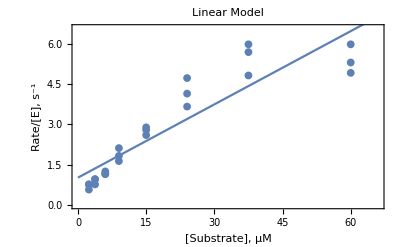

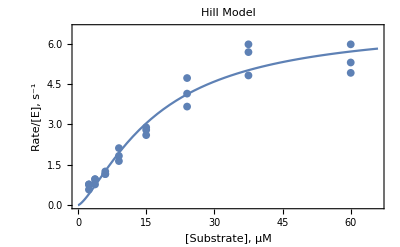

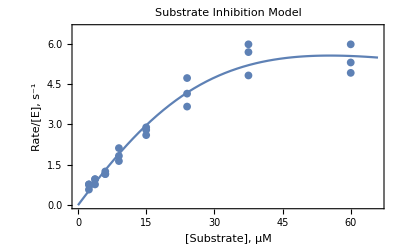

```mathematica
Show[ListPlot[{fullData},PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{LinearModel[S]},{S,0,sMax}],LabelStyle->Directive[Bold,12],PlotLabel->"Linear Model"]
Show[ListPlot[{fullData},PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{HillModel[S]},{S,0,sMax}],LabelStyle->Directive[Bold,12],PlotLabel->"Hill Model"]
Show[ListPlot[{fullData},PlotRange->{{0,sMax},{0,1.1*Max[fullData[[All,2]]]}},PlotMarkers->{Automatic,8},Frame->True,FrameLabel->{"[Substrate], μM","Rate/[E], s^-1"}],Plot[{SubInhModel[S]},{S,0,sMax}],LabelStyle->Directive[Bold,12],PlotLabel->"Substrate Inhibition Model"]
```